Jonas Neundorf & Jan Skottke

# Blatt 5 - Optimierung der Emittanz im DBA-Lattice

Definiere Konstanten

```mathematica
constants={c-> 3.*10^8, q-> 1.602*10^-19,m-> 0.511*10^-3,r0-> 2.818*10^-15,cq-> 3.8*10^-13};
```

## Vorbereitungen

#### Berechnung der Dispersionfunktion

Definiere die Matritzen für die Magnete:

```mathematica
mF[f_]:={{1,0,0},{-1/f,1,0},{0,0,1}} (*fokussierender Quad*)
```

```mathematica
mD[s_, ρ_] := {{Cos[s/ρ], ρ*Sin[s/ρ], ρ*(1 - Cos[s/ρ])}, {-1/ρ*Sin[s/ρ], Cos[s/ρ], Sin[s/ρ]}, {0, 0, 1}}(*Dipol*)
```

Definiere Dispersionsfunktionen:

```mathematica
η[s_]:=ρ*(1-Cos[s/ρ])
```

```mathematica
dη[s_]=D[η[s],s];
```

Die Dispersion soll nach durchqueren des DBA sich nicht geändert haben. Aus dieser Bedingung lässt sich die Brennweite bestimmen.

```mathematica
eq={0,0,1}==mD[L,ρ].mF[f].mD[L,ρ].{η[0],dη[0],1}//FullSimplify
```

{0,0,1}=={(ρ (2 f-2 f Cos[(2 L)/ρ]-2 ρ Sin[L/ρ]+ρ Sin[(2 L)/ρ]))/(2 f),(Cos[L/ρ] (ρ (-1+Cos[L/ρ])+2 f Sin[L/ρ]))/f,1}

```mathematica
focus=Solve[eq,f]//Flatten
```

{f→1/2 ρ Tan[L/(2 ρ)]}

Diese Brennweite muss der Quadropol haben, damit die Dispersion am Ende wieder bei {0,0,1} ist.

#### Tests

Übernehmen wir nun für den Test gleich die Parameter der ESRF

```mathematica
para={ρ-> L/θ,L-> 1.96, θ-> 0.0984,γrel-> 6000/0.511};
```

```mathematica
mD[L,ρ].mF[f].mD[L,ρ].{η[0],dη[0],1}//.focus//FullSimplify
```

{0,0,1}

Die berechnete Brennweite liefert tatsächlich das gewünschte Ergebnis, dass die Dispersion nach dem 2. Dipol wieder bei {0,0,1} ist.

Dispersion nach dem ersten Dipol:

```mathematica
dispd1=mD[L,ρ].{η[0],dη[0],1}//FullSimplify
```

{ρ-ρ Cos[L/ρ],Sin[L/ρ],1}

Dispersion direkt nach dem Quadropol und dem ersten Dipol

```mathematica
dispqd2=mF[f].mD[L,ρ].{η[0],dη[0],1}//.focus//FullSimplify
```

{ρ-ρ Cos[L/ρ],-Sin[L/ρ],1}

Es ändert sich nur das Vorzeichen von η’.

Definieren wir nun η und η’ im gesamten DBA:

```mathematica
fullη[s_] := Piecewise[ {{(mD[s,ρ].{0, 0, 1})[[1]], s <= L},{(mD[s-L, ρ].mF[f].mD[L, ρ].{0, 0, 1})[[1]], L < s≤ 2*L}}]
```

```mathematica
fulldη[s_] := Piecewise[ {{(mD[s,ρ].{0, 0, 1})[[2]], s <= L},{(mD[s-L, ρ].mF[f].mD[L, ρ].{0, 0, 1})[[2]], L < s≤ 2*L}}]
```

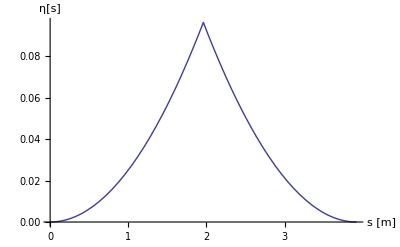

```mathematica
Plot[fullη[s] //.focus //.para, {s, 0, 2L//.para}, AxesLabel->{"s [m]", "η[s]"}]
```

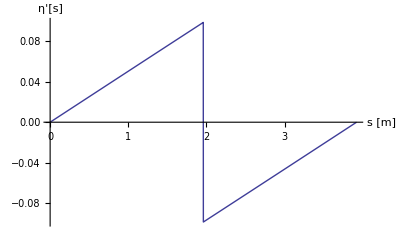

```mathematica
Plot[fulldη[s] //.focus //.para, {s, 0, 2L//.para}, AxesLabel-> {"s [m]", "η'[s]"}]
```

#### Berechnung der Twiss Parameter (β-Funktionen)

```mathematica
bmat={{β0,-α0},{-α0,γ0}}
```

{{β0,-α0},{-α0,γ0}}

```mathematica
drift[s_]:={{1,s},{0,1}}
```

```mathematica
quad[f_]:={{1,0},{-1/f,1}}
```

Zuerst berechnen wir die Parameter für den ersten Dipol:

```mathematica
twissd1[s_]=drift[s].bmat.Transpose[drift[s]]//FullSimplify
```

{{-2 s α0+β0+s^2 γ0,-α0+s γ0},{-α0+s γ0,γ0}}

Nun zur Berechnung der Twissparameter für den letzten Teil, also für den Quadropol und dem zweiten Dipol:

```mathematica
twissqd2[s_]=drift[s-L].quad[f].(twissd1[L]).Transpose[drift[s-L].quad[f]] //.focus //FullSimplify
```

{{-2 s α0+β0+s^2 γ0+(4 (L-s) Cot[L/(2 ρ)] ((-(L+s) α0+β0+L s γ0) ρ+(L-s) (-2 L α0+β0+L^2 γ0) Cot[L/(2 ρ)]))/ρ^2,-α0+s γ0+(2 Cot[L/(2 ρ)] ((2 s α0-β0+L (L-2 s) γ0) ρ+2 (-L+s) (-2 L α0+β0+L^2 γ0) Cot[L/(2 ρ)]))/ρ^2},{-α0+s γ0+(2 Cot[L/(2 ρ)] ((2 s α0-β0+L (L-2 s) γ0) ρ+2 (-L+s) (-2 L α0+β0+L^2 γ0) Cot[L/(2 ρ)]))/ρ^2,(γ0 ρ^2+4 Cot[L/(2 ρ)] ((α0-L γ0) ρ+(-2 L α0+β0+L^2 γ0) Cot[L/(2 ρ)]))/ρ^2}}

```mathematica
β[s_]=Piecewise[{{twissd1[s][[1,1]], s≤ L}, {twissqd2[s][[1,1]], L≤ s≤2*L}}]
```

Piecewise[{{-2 s α0+β0+s^2 γ0, s≤L}, {-2 s α0+β0+s^2 γ0+(4 (L-s) Cot[L/(2 ρ)] ((-(L+s) α0+β0+L s γ0) ρ+(L-s) (-2 L α0+β0+L^2 γ0) Cot[L/(2 ρ)]))/ρ^2, L≤s≤2 L}, {0, True}}]

```mathematica
α[s_]=Piecewise[{{-twissd1[s][[1,2]], s≤ L}, {-twissqd2[s][[1,2]], L≤ s≤2*L}}]
```

Piecewise[{{α0-s γ0, s≤L}, {α0-s γ0-(2 Cot[L/(2 ρ)] ((2 s α0-β0+L (L-2 s) γ0) ρ+2 (-L+s) (-2 L α0+β0+L^2 γ0) Cot[L/(2 ρ)]))/ρ^2, L≤s≤2 L}, {0, True}}]

```mathematica
γ[s_]=Piecewise[{{twissd1[s][[2,2]], s<=L}, {twissqd2[s][[2,2]], L≤ s≤2*L}}]
```

Piecewise[{{γ0, s≤L}, {(γ0 ρ^2+4 Cot[L/(2 ρ)] ((α0-L γ0) ρ+(-2 L α0+β0+L^2 γ0) Cot[L/(2 ρ)]))/ρ^2, L≤s≤2 L}, {0, True}}]

#### Berechnung der Funktion ℋ

Als Hinweis: das eigentliche η in der Gleichung (siehe Aufgabenblatt) wird hier durch fullη und η' wird durch fulldη ersetzt.

```mathematica
ℋ[s_]:=PiecewiseExpand[γ[s]*(fullη[s])^2]+2*PiecewiseExpand[α[s]*fullη[s]*fulldη[s]]+PiecewiseExpand[β[s]*(fulldη[s])^2]
```

## Berechnung und Optimierung der Emittanz

```mathematica
parastart={γ0-> (1+α0^2)/β0,β0-> 2*√(3/5)*L,α0-> √15};
```

#### Die Twiss-Parameter

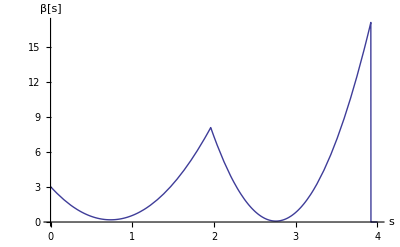

```mathematica
Plot[β[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "β[s]"}]
```

```mathematica
f//.focus//.para
```

0.490396

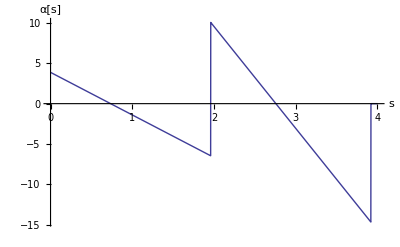

```mathematica
Plot[α[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "α[s]"}]
```

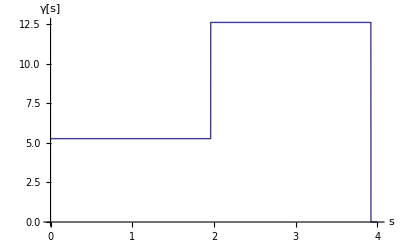

```mathematica
Plot[γ[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "γ[s]"}]
```

Da aus den DBA eine periodische Struktur entsteht, sollten die Twiss-Parameter an Anfang und Ende gleich sein -- was sie offensichtlich nicht sind.

#### Die Funktion ℋ

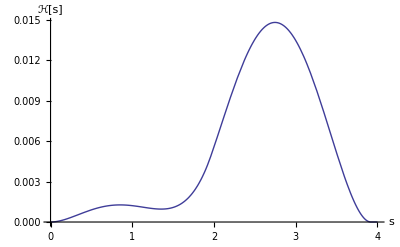

```mathematica
Plot[ℋ[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "ℋ[s]"}]
```

#### Richtige Optimierung

```mathematica
numH[s_]:=ℋ[s]//.focus//.γ0-> (1+α0^2)/β0//.para;//FullSimplify
```

```mathematica
intH=Integrate[numH[s],{s, 0, L//.para}] + Integrate[numH[s], {s, L//.para, 2*L//.para}] //FullSimplify
```

-0.0444697 α0+(0.0241915+0.0241915 α0^2)/β0+0.0214466 β0

```mathematica
nsβ=Solve[D[intH,β0]==0,β0]//FullSimplify (*da β0>0 sein soll, muss man die 2. Lösung nehmen*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{β0→-1.44092×10^-8 √(5.43283×10^15+5.43283×10^15 α0^2)},{β0→1.44092×10^-8 √(5.43283×10^15+5.43283×10^15 α0^2)}}

```mathematica
nsα=Solve[D[intH,α0]==0,α0]//FullSimplify//Flatten
```

{α0→0.919117 β0}

Setzen wir nun diese Parameter ein, um zu gucken was passiert. Wobei, momentan hängen die voneinander ab, das gibt Rekursion bis ins unendliche. Aber wir können ja einfach mal die Rule für α0 als Gleichung auffassen und da dann β0 einsetzen.

```mathematica
αeq = nsα[[1]] //. Rule->Equal //.nsβ[[2,1]]
```

α0==1.32437×10^-8 √(5.43283×10^15+5.43283×10^15 α0^2)

```mathematica
αsol = Solve[αeq, α0] //Flatten
```

{α0→4.49789}

```mathematica
numParams = {γ0-> (1+α0^2)/β0, nsβ[[2,1]], αsol[[1]]}
```

{γ0→(1+α0^2)/β0,β0→1.44092×10^-8 √(5.43283×10^15+5.43283×10^15 α0^2),α0→4.49789}

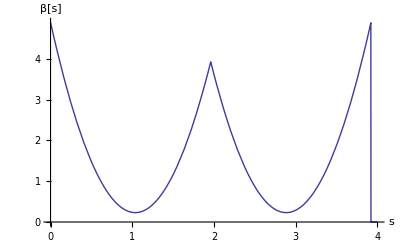

```mathematica
Plot[β[x]//.focus//.numParams//.para, {x, 0, 4}, AxesLabel-> {"s", "β[s]"}]
```

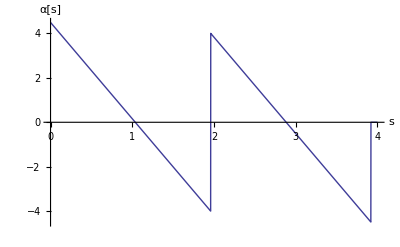

```mathematica
Plot[α[x]//.focus//.numParams//.para, {x, 0, 4}, AxesLabel-> {"s", "α[s]"}]
```

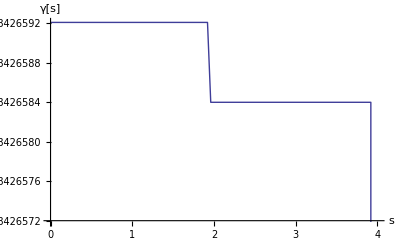

```mathematica
Plot[γ[x]//.focus//.numParams//.para, {x, 0, 4}, AxesLabel-> {"s", "γ[s]"}]
```

Super, α und β sind tatsächlich periodisch. γ nicht, aber da die Werte sich in den beiden Abschnitten praktisch nicht unterscheiden, werden die Stufen einfach ein numerisches Artefakt sein.
Plotten wir nun nochmal ℋ

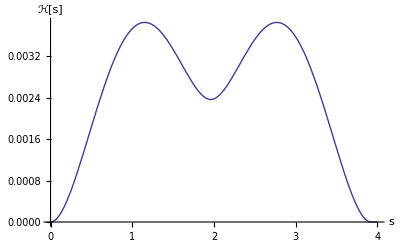

```mathematica
Plot[ℋ[x]//.focus//.numParams//.para, {x, 0, 4}, AxesLabel-> {"s", "ℋ[s]"}]
```

und stellen fest, das auch ℋ auch schön symmetrisch ist.

### Berechnung der Emittanzen und Vergleich

Beginnen wir zunächst mit den kanonischen Parametern.

```mathematica
ϵ = cq * (intH*γrel^2)/(2*L*ρ);
```

```mathematica
Grid[{{"ϵ_kanonisch", ϵ//.parastart //.para//.constants}, {"ϵ_optimiert", ϵ //.numParams //.para//.constants}, {"ϵ_Formel", 1/(4 √15)*cq *γrel^2*θ^3 //.para //.constants}}]
```

ϵ_kanonisch | 1.36637×10^-8
ϵ_optimiert | 6.63366×10^-9
ϵ_Formel | 3.22199×10^-9